```mathematica
(*
Kepler problem:

m d^2\v{r}/dt^2 = -GMm \hat{r}/r^2

if the orbit is in the x-y plane, we can write this as

 d^2x/dt^2 + GMx/(x^2+y^2)^{3/2} = 0

d^2y/dt^2 + GMy/(x^2+y^2)^{3/2} = 0
*)
eps = 1*10^-10;
Vx = Flatten[Table[{i,j,(4Pi^2) i/(i^2+j^2+eps)^(3/2)},{i,-10,10,0.01},{j,-10,10,0.01}],1];
Vy = Flatten[Table[{i,j,(4Pi^2)j/(i^2+j^2+eps)^(3/2)},{i,-10,10,0.01},{j,-10,10,0.01}],1];
iVx = Interpolation[Vx,InterpolationOrder -> 3];
iVy = Interpolation[Vy,InterpolationOrder -> 3];
```

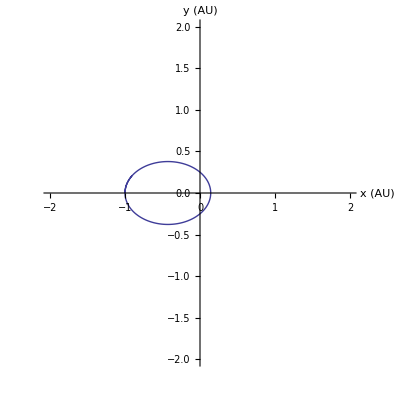

```mathematica
x0 = -1; y0 = 0; x0p = 0; y0p =Pi; tf = 0.5;
Norbit=NDSolve[{x''[t]+iVx[x[t],y[t]]==0,
y''[t]+iVy[x[t],y[t]]==0,
x[0]==x0,y[0]==y0,
x'[0]==x0p,y'[0]==y0p},
{x,y},{t,0,tf}];
(*Aorbit=NDSolve[{x''[t]+(4 Pi^2) x[t]/(x[t]^2+y[t]^2)^(3/2)==0,
y''[t]+(4 Pi^2) y[t]/(x[t]^2+y[t]^2)^(3/2)==0,
x[0]==x0,y[0]==y0,
x'[0]==x0p,y'[0]==y0p},
{x,y},{t,0,tf}];*)
(*Manipulate[ParametricPlot[{Evaluate[{x[t],y[t]}/.Aorbit],Evaluate[{x[t],y[t]}/.Norbit]},{t,0,t0},AxesLabel->{"x (AU)"," y (AU)"}, PlotRange -> {{-2,2},{-2,2}}],{t0,0.05,tf}]*)
(*ParametricPlot[{Evaluate[{x[t],y[t]}/.Aorbit],Evaluate[{x[t],y[t]}/.Norbit]},{t,0,tf},AxesLabel->{"x (AU)"," y (AU)"}, PlotRange -> {{-2,2},{-2,2}}]*)
ParametricPlot[Evaluate[{x[t],y[t]}/.Norbit],{t,0,tf},AxesLabel->{"x (AU)"," y (AU)"}, PlotRange -> {{-2,2},{-2,2}}]
```